# Übungsblatt 4

## Aufgabe 1

(d)

```mathematica
t68=0.0006491525423728814;
t95=0.0001;
normfaktor=483.5684923614078;
sigma={{1.32511440*10^3,-1.96185181*10^1},{-1.96185181*10^1,3.54994215*10^(-1)}};
betaerw={-20.86055019,77.97080866};(*bis hierhin aus Python*)
(*daten68=Import["C:/Users/olive/bwSyncShare/Documents/Dokumente/Physik/5. Semester/Programmieren und Rechnernutzung/Bayes-Statistik/t68.csv"];
daten95=Import["C:/Users/olive/bwSyncShare/Documents/Dokumente/Physik/5. Semester/Programmieren und Rechnernutzung/Bayes-Statistik/t95.csv"];*)
```

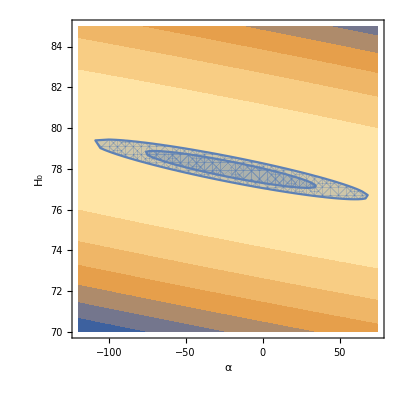

```mathematica
posterior[alpha_,H0_]:=1/normfaktor*Exp[-1/2*({alpha,H0}-betaerw).Inverse[sigma].({alpha,H0}-betaerw)];
contour=ContourPlot[Log[posterior[alpha,H0]],{alpha,-120,75},{H0,70,85},ContourStyle->None];
region1=RegionPlot[posterior[alpha,H0]>t68,{alpha,-120,75},{H0,70,85}];
region2=RegionPlot[posterior[alpha,H0]>t95,{alpha,-120,75},{H0,70,85}];
Show[contour,region2,region1,FrameLabel->{"α","H_0"}]
```